```mathematica
Nt = 551;
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx = 551; 
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)
k = .;
j  = .;
```

1/(2 π)

```mathematica
T = Table[tn = ti + n *deltat, {n, 0, Nt -1 }];
X =  Table[xm = xi + m *deltax, {m, 0, Nx -1}];

T = N[T,32];
X = N[X,32];

h = (2π) / Nx;



D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D1//MatrixForm
```

(1)
 |  |  |  |

```mathematica
f[x_] =ⅇ^(- 4(x-π)^2)
```

ⅇ^(-4 (-π+x)^2)

```mathematica
F = f[X];
```

```mathematica
F' = f'[X];
```

```mathematica
D1.F;
```

```mathematica
Abs[D1.F - f'[X]]
```

{1.798791968668×10^-16,6.92186502176×10^-17,4.069470707761×10^-17,2.84163207709×10^-17,2.17231455087×10^-17,1.75460084746×10^-17,1.47019561895×10^-17,1.26449084837×10^-17,1.10897364069×10^-17,9.87361878599×10^-18,8.89703441808×10^-18,8.09581694855×10^-18,7.42677679185×10^-18,6.85979662274×10^-18,6.37324367242×10^-18,5.95118396927×10^-18,5.58162479363×10^-18,5.25536885698×10^-18,4.9652457384×10^-18,4.70558337161×10^-18,4.47183653043×10^-18,4.26032052187×10^-18,4.06801692571×10^-18,3.89242964046×10^-18,3.73147667738×10^-18,3.58340776475×10^-18,3.44674085912×10^-18,3.32021269155×10^-18,3.2027398598×10^-18,3.0933879345×10^-18,2.9913467174×10^-18,2.895910271×10^-18,2.8064606775×10^-18,2.7224547415×10^-18,2.6434130311×10^-18,2.5689107923×10^-18,2.4985703737×10^-18,2.4320548749×10^-18,2.3690627973×10^-18,2.3093235136×10^-18,2.2525934174×10^-18,2.1986526335×10^-18,2.1473021978×10^-18,2.0983616301×10^-18,2.051666837×10^-18,2.0070682936×10^-18,1.9644294626×10^-18,1.9236254147×10^-18,1.8845416206×10^-18,1.8470728915×10^-18,1.8111224463×10^-18,1.776601088×10^-18,1.7434264752×10^-18,1.7115224767×10^-18,1.6808185963×10^-18,1.6512494615×10^-18,1.6227543667×10^-18,1.5952768634×10^-18,1.5687643945×10^-18,1.5431679641×10^-18,1.5184418415×10^-18,1.4945432933×10^-18,1.4714323423×10^-18,1.4490715487×10^-18,1.4274258122×10^-18,1.4064621918×10^-18,1.3861497428×10^-18,1.3664593676×10^-18,1.3473636802×10^-18,1.328836882×10^-18,1.3108546489×10^-18,1.2933940269×10^-18,1.2764333377×10^-18,1.2599520909×10^-18,1.243930904×10^-18,1.2283514285×10^-18,1.213196282×10^-18,1.1984489855×10^-18,1.1840939052×10^-18,1.1701161997×10^-18,1.1565017698×10^-18,1.1432372132×10^-18,1.1303097818×10^-18,1.1177073425×10^-18,1.1054183402×10^-18,1.0934317644×10^-18,1.0817371171×10^-18,1.0703243836×10^-18,1.0591840049×10^-18,1.0483068522×10^-18,1.0376842031×10^-18,1.0273077192×10^-18,1.017169425×10^-18,1.007261689×10^-18,9.9757720485×10^-19,9.8810897438×10^-19,9.7885029177×10^-19,9.697947283×10^-19,9.6093611827×10^-19,9.5226854575×10^-19,9.4378633207×10^-19,9.3548402408×10^-19,9.2735638316×10^-19,9.1939837473×10^-19,9.1160515853×10^-19,9.0397207932×10^-19,8.9649465818×10^-19,8.891685843×10^-19,8.8198970715×10^-19,8.749540292×10^-19,8.6805769895×10^-19,8.6129700432×10^-19,8.5466836649×10^-19,8.48168334×10^-19,8.4179357714×10^-19,8.3554088271×10^-19,8.2940714895×10^-19,8.2338938084×10^-19,8.1748468555×10^-19,8.1169026818×10^-19,8.0600342767×10^-19,8.0042155291×10^-19,7.9494211911×10^-19,7.8956268426×10^-19,7.8428088582×10^-19,7.7909443753×10^-19,7.7400112642×10^-19,7.6899880989×10^-19,7.6408541301×10^-19,7.5925892589×10^-19,7.5451740118×10^-19,7.4985895168×10^-19,7.4528174811×10^-19,7.407840169×10^-19,7.3636403814×10^-19,7.3202014358×10^-19,7.2775071477×10^-19,7.2355418124×10^-19,7.1942901874×10^-19,7.1537374762×10^-19,7.1138693125×10^-19,7.0746717446×10^-19,7.0361312213×10^-19,6.9982345779×10^-19,6.9609690227×10^-19,6.9243221244×10^-19,6.8882817997×10^-19,6.8528363016×10^-19,6.8179742083×10^-19,6.783684412×10^-19,6.7499561088×10^-19,6.7167787889×10^-19,6.6841422265×10^-19,6.6520364709×10^-19,6.6204518379×10^-19,6.5893789008×10^-19,6.5588084827×10^-19,6.5287316481×10^-19,6.499139696×10^-19,6.4700241522×10^-19,6.4413767623×10^-19,6.4131894854×10^-19,6.3854544868×10^-19,6.3581641327×10^-19,6.3313109836×10^-19,6.3048877886×10^-19,6.27888748×10^-19,6.253303167×10^-19,6.228128134×10^-19,6.203355828×10^-19,6.178979864×10^-19,6.154994012×10^-19,6.131392196×10^-19,6.10816849×10^-19,6.085317112×10^-19,6.062832421×10^-19,6.040708915×10^-19,6.018941223×10^-19,5.997524105×10^-19,5.976452448×10^-19,5.955721259×10^-19,5.935325668×10^-19,5.915260919×10^-19,5.895522371×10^-19,5.876105491×10^-19,5.857005857×10^-19,5.838219148×10^-19,5.819741148×10^-19,5.80156774×10^-19,5.783694902×10^-19,5.766118709×10^-19,5.748835327×10^-19,5.731841012×10^-19,5.715132109×10^-19,5.698705047×10^-19,5.682556339×10^-19,5.666682581×10^-19,5.651080446×10^-19,5.635746688×10^-19,5.620678134×10^-19,5.605871688×10^-19,5.591324324×10^-19,5.577033089×10^-19,5.562995099×10^-19,5.549207535×10^-19,5.535667649×10^-19,5.522372755×10^-19,5.509320229×10^-19,5.496507513×10^-19,5.483932106×10^-19,5.47159157×10^-19,5.459483521×10^-19,5.447605637×10^-19,5.435955647×10^-19,5.424531339×10^-19,5.413330551×10^-19,5.402351176×10^-19,5.391591158×10^-19,5.381048492×10^-19,5.370721221×10^-19,5.360607438×10^-19,5.350705284×10^-19,5.341012946×10^-19,5.331528657×10^-19,5.322250697×10^-19,5.313177387×10^-19,5.304307096×10^-19,5.295638232×10^-19,5.287169248×10^-19,5.278898637×10^-19,5.270824932×10^-19,5.262946708×10^-19,5.255262579×10^-19,5.247771197×10^-19,5.240471254×10^-19,5.233361477×10^-19,5.226440633×10^-19,5.219707523×10^-19,5.213160987×10^-19,5.206799899×10^-19,5.200623167×10^-19,5.194629735×10^-19,5.188818582×10^-19,5.183188719×10^-19,5.177739191×10^-19,5.172469077×10^-19,5.167377487×10^-19,5.162463563×10^-19,5.157726481×10^-19,5.153165446×10^-19,5.148779696×10^-19,5.144568499×10^-19,5.140531153×10^-19,5.136666987×10^-19,5.13297536×10^-19,5.12945566×10^-19,5.126107306×10^-19,5.122929745×10^-19,5.119922452×10^-19,5.117084934×10^-19,5.114416722×10^-19,5.11191738×10^-19,5.109586497×10^-19,5.107423693×10^-19,5.105428612×10^-19,5.103600928×10^-19,5.101940344×10^-19,5.100446589×10^-19,5.099119418×10^-19,5.097958615×10^-19,5.096963992×10^-19,5.096135387×10^-19,5.095472664×10^-19,5.094975716×10^-19,5.094644462×10^-19,5.094478849×10^-19,5.094478849×10^-19,5.094644462×10^-19,5.094975716×10^-19,5.095472664×10^-19,5.096135387×10^-19,5.096963992×10^-19,5.097958615×10^-19,5.099119418×10^-19,5.100446589×10^-19,5.101940344×10^-19,5.103600928×10^-19,5.105428612×10^-19,5.107423693×10^-19,5.109586497×10^-19,5.11191738×10^-19,5.114416722×10^-19,5.117084934×10^-19,5.119922452×10^-19,5.122929745×10^-19,5.126107306×10^-19,5.12945566×10^-19,5.13297536×10^-19,5.136666987×10^-19,5.140531153×10^-19,5.144568499×10^-19,5.148779696×10^-19,5.153165446×10^-19,5.157726481×10^-19,5.162463563×10^-19,5.167377487×10^-19,5.172469077×10^-19,5.177739191×10^-19,5.183188719×10^-19,5.188818582×10^-19,5.194629735×10^-19,5.200623167×10^-19,5.206799899×10^-19,5.213160987×10^-19,5.219707523×10^-19,5.226440633×10^-19,5.233361477×10^-19,5.240471254×10^-19,5.247771197×10^-19,5.255262579×10^-19,5.262946708×10^-19,5.270824932×10^-19,5.278898637×10^-19,5.287169248×10^-19,5.295638232×10^-19,5.304307096×10^-19,5.313177387×10^-19,5.322250697×10^-19,5.331528657×10^-19,5.341012946×10^-19,5.350705284×10^-19,5.360607438×10^-19,5.370721221×10^-19,5.381048492×10^-19,5.391591158×10^-19,5.402351176×10^-19,5.413330551×10^-19,5.424531339×10^-19,5.435955647×10^-19,5.447605637×10^-19,5.459483521×10^-19,5.47159157×10^-19,5.483932106×10^-19,5.496507513×10^-19,5.509320229×10^-19,5.522372755×10^-19,5.535667649×10^-19,5.549207535×10^-19,5.562995099×10^-19,5.577033089×10^-19,5.591324324×10^-19,5.605871688×10^-19,5.620678134×10^-19,5.635746688×10^-19,5.651080446×10^-19,5.666682581×10^-19,5.682556339×10^-19,5.698705047×10^-19,5.715132109×10^-19,5.731841012×10^-19,5.748835327×10^-19,5.766118709×10^-19,5.783694902×10^-19,5.80156774×10^-19,5.819741148×10^-19,5.838219148×10^-19,5.857005857×10^-19,5.876105491×10^-19,5.895522371×10^-19,5.915260919×10^-19,5.935325668×10^-19,5.955721259×10^-19,5.976452448×10^-19,5.997524105×10^-19,6.018941223×10^-19,6.040708915×10^-19,6.062832421×10^-19,6.085317112×10^-19,6.10816849×10^-19,6.131392196×10^-19,6.154994012×10^-19,6.178979864×10^-19,6.203355828×10^-19,6.228128134×10^-19,6.253303167×10^-19,6.27888748×10^-19,6.304887789×10^-19,6.331310984×10^-19,6.358164133×10^-19,6.385454487×10^-19,6.413189485×10^-19,6.441376762×10^-19,6.470024152×10^-19,6.499139696×10^-19,6.5287316481×10^-19,6.5588084827×10^-19,6.5893789008×10^-19,6.6204518379×10^-19,6.6520364709×10^-19,6.6841422265×10^-19,6.7167787889×10^-19,6.7499561088×10^-19,6.783684412×10^-19,6.8179742083×10^-19,6.8528363016×10^-19,6.8882817997×10^-19,6.9243221244×10^-19,6.9609690227×10^-19,6.9982345779×10^-19,7.0361312213×10^-19,7.0746717446×10^-19,7.1138693125×10^-19,7.1537374762×10^-19,7.1942901874×10^-19,7.2355418124×10^-19,7.2775071477×10^-19,7.3202014358×10^-19,7.3636403814×10^-19,7.407840169×10^-19,7.4528174811×10^-19,7.4985895168×10^-19,7.5451740118×10^-19,7.5925892589×10^-19,7.6408541301×10^-19,7.6899880989×10^-19,7.7400112642×10^-19,7.7909443753×10^-19,7.8428088582×10^-19,7.8956268426×10^-19,7.9494211911×10^-19,8.0042155291×10^-19,8.0600342767×10^-19,8.1169026818×10^-19,8.1748468555×10^-19,8.2338938084×10^-19,8.2940714895×10^-19,8.3554088271×10^-19,8.4179357714×10^-19,8.48168334×10^-19,8.5466836649×10^-19,8.6129700432×10^-19,8.6805769895×10^-19,8.749540292×10^-19,8.8198970715×10^-19,8.891685843×10^-19,8.9649465818×10^-19,9.0397207932×10^-19,9.1160515853×10^-19,9.1939837473×10^-19,9.2735638316×10^-19,9.3548402408×10^-19,9.4378633207×10^-19,9.5226854575×10^-19,9.6093611827×10^-19,9.697947283×10^-19,9.7885029177×10^-19,9.8810897438×10^-19,9.9757720485×10^-19,1.007261689×10^-18,1.017169425×10^-18,1.0273077192×10^-18,1.0376842031×10^-18,1.0483068522×10^-18,1.0591840049×10^-18,1.0703243836×10^-18,1.0817371171×10^-18,1.0934317644×10^-18,1.1054183402×10^-18,1.1177073425×10^-18,1.1303097818×10^-18,1.1432372132×10^-18,1.1565017698×10^-18,1.1701161997×10^-18,1.1840939052×10^-18,1.1984489855×10^-18,1.213196282×10^-18,1.2283514285×10^-18,1.243930904×10^-18,1.2599520909×10^-18,1.2764333377×10^-18,1.2933940269×10^-18,1.3108546489×10^-18,1.328836882×10^-18,1.3473636802×10^-18,1.3664593676×10^-18,1.3861497428×10^-18,1.4064621918×10^-18,1.4274258122×10^-18,1.4490715487×10^-18,1.4714323423×10^-18,1.4945432933×10^-18,1.5184418415×10^-18,1.5431679641×10^-18,1.5687643945×10^-18,1.5952768634×10^-18,1.6227543667×10^-18,1.6512494615×10^-18,1.6808185963×10^-18,1.7115224767×10^-18,1.7434264752×10^-18,1.776601088×10^-18,1.8111224463×10^-18,1.8470728915×10^-18,1.8845416206×10^-18,1.9236254147×10^-18,1.9644294626×10^-18,2.0070682936×10^-18,2.051666837×10^-18,2.0983616301×10^-18,2.1473021978×10^-18,2.1986526335×10^-18,2.2525934174×10^-18,2.3093235136×10^-18,2.3690627973×10^-18,2.4320548749×10^-18,2.4985703737×10^-18,2.5689107923×10^-18,2.6434130311×10^-18,2.7224547415×10^-18,2.8064606775×10^-18,2.895910271×10^-18,2.9913467174×10^-18,3.0933879345×10^-18,3.2027398598×10^-18,3.32021269155×10^-18,3.44674085912×10^-18,3.58340776475×10^-18,3.73147667738×10^-18,3.89242964046×10^-18,4.06801692571×10^-18,4.26032052187×10^-18,4.47183653043×10^-18,4.70558337161×10^-18,4.9652457384×10^-18,5.25536885698×10^-18,5.58162479363×10^-18,5.95118396927×10^-18,6.37324367242×10^-18,6.85979662274×10^-18,7.42677679185×10^-18,8.09581694855×10^-18,8.89703441808×10^-18,9.87361878599×10^-18,1.10897364069×10^-17,1.26449084837×10^-17,1.47019561895×10^-17,1.75460084746×10^-17,2.17231455087×10^-17,2.84163207709×10^-17,4.069470707761×10^-17,6.92186502176×10^-17}

```mathematica
Max[Abs[D1.F - f'[X]]]
```

1.798791968668×10^-16

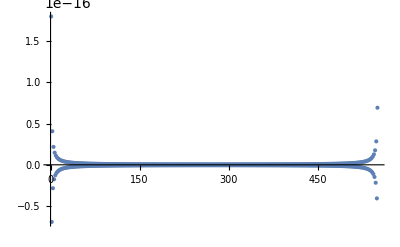

```mathematica
ListPlot[f'[X] - D1.F, PlotRange->All]
```

```mathematica
f[x_] =ⅇ^(- 8(x-π)^2)
```

ⅇ^(-8 (-π+x)^2)

```mathematica
F = f[X];
```

```mathematica
F' = f'[X];
```

```mathematica
D1.F;
```

```mathematica
Abs[D1.F - f'[X]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.×10^-30,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.×10^-30,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Max[Abs[D1.F - f'[X]]]
```

4.×10^-30

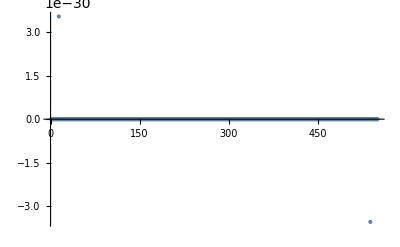

```mathematica
ListPlot[f'[X] - D1.F, PlotRange->All]
```